# Density of state

```mathematica
(*Equation of motion?*)
M=Flatten[Table[D[Subscript[ρ, n,m][t],t]==-I (Subscript[w, En][n,m])Subscript[ρ, n,m]+I/ℏ Sum[Subscript[d, n,v] Ε[n,v] Subscript[ρ, v,m]-Subscript[ρ, n,v] Subscript[d, v,m] Ε[v,m],{v,1,3}]+If[n≠m,-Subscript[γ, n,m] Subscript[ρ, n,m],Sum[If[n≥ 3,-Γ[v,n] Subscript[ρ, n,n],Γ[n,v] Subscript[ρ, v,v]],{v,1,3}]],{n,1,3},{m,1,3}]//Expand,1];
%//TableForm
```

ρ_(1,1)'[t]==ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+(ⅈ d_(1,2) ρ_(2,1) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,1) Ε[1,3])/ℏ-(ⅈ d_(2,1) ρ_(1,2) Ε[2,1])/ℏ-(ⅈ d_(3,1) ρ_(1,3) Ε[3,1])/ℏ-ⅈ ρ_(1,1) w_En[1,1]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)+(ⅈ d_(1,1) ρ_(1,2) Ε[1,1])/ℏ-(ⅈ d_(1,2) ρ_(1,1) Ε[1,2])/ℏ+(ⅈ d_(1,2) ρ_(2,2) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,2) Ε[1,3])/ℏ-(ⅈ d_(2,2) ρ_(1,2) Ε[2,2])/ℏ-(ⅈ d_(3,2) ρ_(1,3) Ε[3,2])/ℏ-ⅈ ρ_(1,2) w_En[1,2]
ρ_(1,3)'[t]==-γ_(1,3) ρ_(1,3)+(ⅈ d_(1,1) ρ_(1,3) Ε[1,1])/ℏ+(ⅈ d_(1,2) ρ_(2,3) Ε[1,2])/ℏ-(ⅈ d_(1,3) ρ_(1,1) Ε[1,3])/ℏ+(ⅈ d_(1,3) ρ_(3,3) Ε[1,3])/ℏ-(ⅈ d_(2,3) ρ_(1,2) Ε[2,3])/ℏ-(ⅈ d_(3,3) ρ_(1,3) Ε[3,3])/ℏ-ⅈ ρ_(1,3) w_En[1,3]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-(ⅈ d_(1,1) ρ_(2,1) Ε[1,1])/ℏ+(ⅈ d_(2,1) ρ_(1,1) Ε[2,1])/ℏ-(ⅈ d_(2,1) ρ_(2,2) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,1) Ε[2,2])/ℏ+(ⅈ d_(2,3) ρ_(3,1) Ε[2,3])/ℏ-(ⅈ d_(3,1) ρ_(2,3) Ε[3,1])/ℏ-ⅈ ρ_(2,1) w_En[2,1]
ρ_(2,2)'[t]==ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]-(ⅈ d_(1,2) ρ_(2,1) Ε[1,2])/ℏ+(ⅈ d_(2,1) ρ_(1,2) Ε[2,1])/ℏ+(ⅈ d_(2,3) ρ_(3,2) Ε[2,3])/ℏ-(ⅈ d_(3,2) ρ_(2,3) Ε[3,2])/ℏ-ⅈ ρ_(2,2) w_En[2,2]
ρ_(2,3)'[t]==-γ_(2,3) ρ_(2,3)-(ⅈ d_(1,3) ρ_(2,1) Ε[1,3])/ℏ+(ⅈ d_(2,1) ρ_(1,3) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,3) Ε[2,2])/ℏ-(ⅈ d_(2,3) ρ_(2,2) Ε[2,3])/ℏ+(ⅈ d_(2,3) ρ_(3,3) Ε[2,3])/ℏ-(ⅈ d_(3,3) ρ_(2,3) Ε[3,3])/ℏ-ⅈ ρ_(2,3) w_En[2,3]
ρ_(3,1)'[t]==-γ_(3,1) ρ_(3,1)-(ⅈ d_(1,1) ρ_(3,1) Ε[1,1])/ℏ-(ⅈ d_(2,1) ρ_(3,2) Ε[2,1])/ℏ+(ⅈ d_(3,1) ρ_(1,1) Ε[3,1])/ℏ-(ⅈ d_(3,1) ρ_(3,3) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,1) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,1) Ε[3,3])/ℏ-ⅈ ρ_(3,1) w_En[3,1]
ρ_(3,2)'[t]==-γ_(3,2) ρ_(3,2)-(ⅈ d_(1,2) ρ_(3,1) Ε[1,2])/ℏ-(ⅈ d_(2,2) ρ_(3,2) Ε[2,2])/ℏ+(ⅈ d_(3,1) ρ_(1,2) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,2) Ε[3,2])/ℏ-(ⅈ d_(3,2) ρ_(3,3) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,2) Ε[3,3])/ℏ-ⅈ ρ_(3,2) w_En[3,2]
ρ_(3,3)'[t]==-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-(ⅈ d_(1,3) ρ_(3,1) Ε[1,3])/ℏ-(ⅈ d_(2,3) ρ_(3,2) Ε[2,3])/ℏ+(ⅈ d_(3,1) ρ_(1,3) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,3) Ε[3,2])/ℏ-ⅈ ρ_(3,3) w_En[3,3]

```mathematica
(*Applying Electric field is E Exp[-Iwt]*)
Subscript[w, En][n_,m_]:=If[n>m,w[n,m],-w[m,n]]
Subscript[w, Ex][i_,j_]:=If[i>j,Subscript[w, Ext][i,j],-Subscript[w, Ext][j,i]]
M1=M/.Flatten[Table[ Ε[i,j]->E0[i,j]Exp[-I Subscript[w, Ex][i,j]t],{i,1,4},{j,1,4}]];
%//TableForm
```

ρ_(1,1)'[t]==-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,1))/ℏ+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]
ρ_(1,2)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(1,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(1,2))/ℏ-γ_(1,2) ρ_(1,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(1,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,2))/ℏ+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(1,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(1,3))/ℏ-γ_(1,3) ρ_(1,3)+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,3))/ℏ+ⅈ ρ_(1,3) w[3,1]
ρ_(2,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,1))/ℏ-γ_(2,1) ρ_(2,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(2,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,1))/ℏ-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,1))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,2))/ℏ+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]
ρ_(2,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(2,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(2,3))/ℏ-γ_(2,3) ρ_(2,3)+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,3))/ℏ+ⅈ ρ_(2,3) w[3,2]
ρ_(3,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,1))/ℏ-γ_(3,1) ρ_(3,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(3,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(3,3))/ℏ-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,2))/ℏ-γ_(3,2) ρ_(3,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(3,3))/ℏ-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,2))/ℏ+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]

```mathematica
(*In terms of rabi frequency*)
M2=M1/.{Subscript[d, 3,1]->(ℏ Ω31)/(2 E0[3,1]),Subscript[d, 1,3]->(ℏ Ω13)/(2 E0[1,3]),Subscript[d, 4,1]->(ℏ Ω41)/(2 E0[4,1]),Subscript[d, 1,4]->(ℏ Ω14)/(2 E0[1,4]),Subscript[d, 3,2]->(ℏ Ω32)/(2 E0[3,2]),Subscript[d, 2,3]->(ℏ Ω23)/(2 E0[2,3]),Subscript[d, 4,2]->(ℏ Ω42)/(2 E0[4,2]),Subscript[d, 2,4]->(ℏ Ω24)/(2 E0[2,4]),Subscript[d, 1,2]->(ℏ Ω12)/(2 E0[1,2]),Subscript[d, 2,1]->(ℏ Ω21)/(2 E0[2,1]),Subscript[d, 3,4]->(ℏ Ω34)/(2 E0[3,4]),Subscript[d, 4,3]->(ℏ Ω43)/(2 E0[4,3])};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]
ρ_(1,2)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(1,1)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(1,2))/ℏ-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(1,3))/ℏ-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(2,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,1))/ℏ-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(2,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]
ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(2,3))/ℏ-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,1))/ℏ-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(3,1)-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,2))/ℏ-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]

```mathematica
(*There is no dipole and w to themselves*)
M3=M2/.{Subscript[d, 1,1]->0,Subscript[d, 2,2]->0,Subscript[d, 3,3]->0,Subscript[d, 4,4]->0,Subscript[w, 1,1]->0,Subscript[w, 2,2]->0,Subscript[w, 3,3]->0,Subscript[w, 4,4]->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]
ρ_(1,2)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(1,1)-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(2,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,1)-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(2,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]
ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(3,1)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]

```mathematica
(*Limit 3->4 and 1->2 process*)
M4=M3/.{Ω21 ->0,Ω12 ->0,Ω34 ->0,Ω43 ->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]
ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]

```mathematica
(*No decay on 3->4 and 1->2, no self decay, no self frequncy*)
M5=M4/.{Γ[2,1]-> 0,Γ[1,2]-> 0,Γ[4,3]-> 0,Γ[3,4]-> 0,Γ[1,1]-> 0,Γ[2,2]-> 0,Γ[3,3]-> 0,Γ[4,4]-> 0,w[1,1]-> 0,w[2,2]->0,w[3,3]->0,w[4,4]->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+ρ_(3,3) Γ[1,3]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ρ_(3,3) Γ[2,3]
ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]

```mathematica
(*Sending it to Rotating frame!*)
opt={
Subscript[w, Ext][1,1]-> 0,Subscript[w, Ext][2,2]->0,Subscript[w, Ext][3,3]->0,Subscript[w, Ext][4,4]->0,(*no freq itself*)
Subscript[w, Ext][2,1]-> Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2],Subscript[w, Ext][4,3]->Subscript[w, Ext][4,2]-Subscript[w, Ext][3,2](*not allowed transition by other transition field*)
};
rot=Flatten[Table[D[Subscript[ρ, i,j][t],t]-> D[Subscript[σ, i,j][t]Exp[-I (Subscript[w, Ex][i,j])t],t],{i,1,3},{j,1,3}]/.opt]
rot1=Flatten[Table[Subscript[ρ, i,j]->Subscript[σ, i,j][t]Exp[-I (Subscript[w, Ex][i,j])t],{i,1,3},{j,1,3}]/.opt]
```

{ρ_(1,1)'[t]→σ_(1,1)'[t],ρ_(1,2)'[t]→ⅈ ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) (w_Ext[3,1]-w_Ext[3,2]) σ_(1,2)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(1,2)'[t],ρ_(1,3)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[3,1]) w_Ext[3,1] σ_(1,3)[t]+ⅇ^(ⅈ t w_Ext[3,1]) σ_(1,3)'[t],ρ_(2,1)'[t]→-ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) (w_Ext[3,1]-w_Ext[3,2]) σ_(2,1)[t]+ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(2,1)'[t],ρ_(2,2)'[t]→σ_(2,2)'[t],ρ_(2,3)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[3,2]) w_Ext[3,2] σ_(2,3)[t]+ⅇ^(ⅈ t w_Ext[3,2]) σ_(2,3)'[t],ρ_(3,1)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) w_Ext[3,1] σ_(3,1)[t]+ⅇ^(-ⅈ t w_Ext[3,1]) σ_(3,1)'[t],ρ_(3,2)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) w_Ext[3,2] σ_(3,2)[t]+ⅇ^(-ⅈ t w_Ext[3,2]) σ_(3,2)'[t],ρ_(3,3)'[t]→σ_(3,3)'[t]}

{ρ_(1,1)→σ_(1,1)[t],ρ_(1,2)→ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(1,2)[t],ρ_(1,3)→ⅇ^(ⅈ t w_Ext[3,1]) σ_(1,3)[t],ρ_(2,1)→ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(2,1)[t],ρ_(2,2)→σ_(2,2)[t],ρ_(2,3)→ⅇ^(ⅈ t w_Ext[3,2]) σ_(2,3)[t],ρ_(3,1)→ⅇ^(-ⅈ t w_Ext[3,1]) σ_(3,1)[t],ρ_(3,2)→ⅇ^(-ⅈ t w_Ext[3,2]) σ_(3,2)[t],ρ_(3,3)→σ_(3,3)[t]}

```mathematica
M6=Flatten[Solve[M5/.rot/.rot1,Flatten[Table[Subscript[σ, i,j]'[t],{i,1,3},{j,1,3}]]]//Simplify];
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ Ω31 σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,1)[t]+Γ[1,3] σ_(3,3)[t]
σ_(1,2)'[t]→1/2 ⅈ (2 ⅈ γ_(1,2) σ_(1,2)[t]+2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(1,2)[t]-Ω32 σ_(1,3)[t]+Ω13 σ_(3,2)[t])
σ_(1,3)'[t]→-1/2 ⅈ (Ω13 σ_(1,1)[t]+Ω23 σ_(1,2)[t]-2 ⅈ γ_(1,3) σ_(1,3)[t]-2 w[3,1] σ_(1,3)[t]+2 w_Ext[3,1] σ_(1,3)[t]-Ω13 σ_(3,3)[t])
σ_(2,1)'[t]→1/2 ⅈ (2 ⅈ γ_(2,1) σ_(2,1)[t]-2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(2,1)[t]-Ω31 σ_(2,3)[t]+Ω23 σ_(3,1)[t])
σ_(2,2)'[t]→-1/2 ⅈ Ω32 σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,2)[t]+Γ[2,3] σ_(3,3)[t]
σ_(2,3)'[t]→-1/2 ⅈ (Ω13 σ_(2,1)[t]+Ω23 σ_(2,2)[t]-2 ⅈ γ_(2,3) σ_(2,3)[t]-2 w[3,2] σ_(2,3)[t]+2 w_Ext[3,2] σ_(2,3)[t]-Ω23 σ_(3,3)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-2 w[3,1] σ_(3,1)[t]+2 w_Ext[3,1] σ_(3,1)[t]-Ω31 σ_(3,3)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-2 w[3,2] σ_(3,2)[t]+2 w_Ext[3,2] σ_(3,2)[t]-Ω32 σ_(3,3)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])

```mathematica
(*Some frequncy algebra*)
M7=M6/.{ⅇ^(ⅈ t (Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2]-Subscript[w, Ext][4,1]+Subscript[w, Ext][4,2]))->1,ⅇ^(ⅈ t (-Subscript[w, Ext][3,1]+Subscript[w, Ext][3,2]+Subscript[w, Ext][4,1]-Subscript[w, Ext][4,2]))->1,(ⅇ^(-ⅈ t (Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2]-Subscript[w, Ext][4,1]+Subscript[w, Ext][4,2])))->1}//Simplify;
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ Ω31 σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,1)[t]+Γ[1,3] σ_(3,3)[t]
σ_(1,2)'[t]→1/2 ⅈ (2 ⅈ γ_(1,2) σ_(1,2)[t]+2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(1,2)[t]-Ω32 σ_(1,3)[t]+Ω13 σ_(3,2)[t])
σ_(1,3)'[t]→-1/2 ⅈ (Ω13 σ_(1,1)[t]+Ω23 σ_(1,2)[t]-2 ⅈ γ_(1,3) σ_(1,3)[t]-2 w[3,1] σ_(1,3)[t]+2 w_Ext[3,1] σ_(1,3)[t]-Ω13 σ_(3,3)[t])
σ_(2,1)'[t]→1/2 ⅈ (2 ⅈ γ_(2,1) σ_(2,1)[t]-2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(2,1)[t]-Ω31 σ_(2,3)[t]+Ω23 σ_(3,1)[t])
σ_(2,2)'[t]→-1/2 ⅈ Ω32 σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,2)[t]+Γ[2,3] σ_(3,3)[t]
σ_(2,3)'[t]→-1/2 ⅈ (Ω13 σ_(2,1)[t]+Ω23 σ_(2,2)[t]-2 ⅈ γ_(2,3) σ_(2,3)[t]-2 w[3,2] σ_(2,3)[t]+2 w_Ext[3,2] σ_(2,3)[t]-Ω23 σ_(3,3)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-2 w[3,1] σ_(3,1)[t]+2 w_Ext[3,1] σ_(3,1)[t]-Ω31 σ_(3,3)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-2 w[3,2] σ_(3,2)[t]+2 w_Ext[3,2] σ_(3,2)[t]-Ω32 σ_(3,3)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])

```mathematica
(*Let's Look at the difference of the frequncy*)
twophoton={w[2,1]-> Subscript[w, Ext][3,1]+Δ1-Subscript[w, Ext][3,2]-Δ3, w[4,3] ->-  Subscript[w, Ext][3,2] -Δ3+ Subscript[w, Ext][4,2]+Δ4};
onephoton={ w[3,1]->  Subscript[w, Ext][3,1]+Δ1,w[4,1] ->  Subscript[w, Ext][4,1]+Δ2,w[3,2]->  Subscript[w, Ext][3,2]+Δ3 , w[4,2] ->  Subscript[w, Ext][4,2] +Δ4};
M8=Simplify[Expand[M7/.twophoton/.onephoton]];
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ Ω31 σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,1)[t]+Γ[1,3] σ_(3,3)[t]
σ_(1,2)'[t]→1/2 ⅈ (2 (Δ1-Δ3+ⅈ γ_(1,2)) σ_(1,2)[t]-Ω32 σ_(1,3)[t]+Ω13 σ_(3,2)[t])
σ_(1,3)'[t]→1/2 ⅈ (-Ω13 σ_(1,1)[t]-Ω23 σ_(1,2)[t]+2 Δ1 σ_(1,3)[t]+2 ⅈ γ_(1,3) σ_(1,3)[t]+Ω13 σ_(3,3)[t])
σ_(2,1)'[t]→-1/2 ⅈ (2 (Δ1-Δ3-ⅈ γ_(2,1)) σ_(2,1)[t]+Ω31 σ_(2,3)[t]-Ω23 σ_(3,1)[t])
σ_(2,2)'[t]→-1/2 ⅈ Ω32 σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,2)[t]+Γ[2,3] σ_(3,3)[t]
σ_(2,3)'[t]→1/2 ⅈ (-Ω13 σ_(2,1)[t]-Ω23 σ_(2,2)[t]+2 Δ3 σ_(2,3)[t]+2 ⅈ γ_(2,3) σ_(2,3)[t]+Ω23 σ_(3,3)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]-2 Δ1 σ_(3,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-Ω31 σ_(3,3)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]-2 Δ3 σ_(3,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-Ω32 σ_(3,3)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])

```mathematica
(*Now make this into two field*)
opt1={Δ2-> w43+Δ1,Δ4-> w43+Δ3,Ω41->Sqrt[7/2]Ω31,Ω14->Sqrt[7/2]Ω13,Ω42->Sqrt[4/5]Ω32,Ω24->Sqrt[4/5]Ω23};
(*Two Photon detuning*)
opt2={Δ3-> δ+Δ1};
M9=M8/.opt2//Expand;
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ Ω31 σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,1)[t]+Γ[1,3] σ_(3,3)[t]
σ_(1,2)'[t]→-ⅈ δ σ_(1,2)[t]-γ_(1,2) σ_(1,2)[t]-1/2 ⅈ Ω32 σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,2)[t]
σ_(1,3)'[t]→-1/2 ⅈ Ω13 σ_(1,1)[t]-1/2 ⅈ Ω23 σ_(1,2)[t]+ⅈ Δ1 σ_(1,3)[t]-γ_(1,3) σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,3)[t]
σ_(2,1)'[t]→ⅈ δ σ_(2,1)[t]-γ_(2,1) σ_(2,1)[t]-1/2 ⅈ Ω31 σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,1)[t]
σ_(2,2)'[t]→-1/2 ⅈ Ω32 σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,2)[t]+Γ[2,3] σ_(3,3)[t]
σ_(2,3)'[t]→-1/2 ⅈ Ω13 σ_(2,1)[t]-1/2 ⅈ Ω23 σ_(2,2)[t]+ⅈ δ σ_(2,3)[t]+ⅈ Δ1 σ_(2,3)[t]-γ_(2,3) σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,3)[t]
σ_(3,1)'[t]→1/2 ⅈ Ω31 σ_(1,1)[t]+1/2 ⅈ Ω32 σ_(2,1)[t]-ⅈ Δ1 σ_(3,1)[t]-γ_(3,1) σ_(3,1)[t]-1/2 ⅈ Ω31 σ_(3,3)[t]
σ_(3,2)'[t]→1/2 ⅈ Ω31 σ_(1,2)[t]+1/2 ⅈ Ω32 σ_(2,2)[t]-ⅈ δ σ_(3,2)[t]-ⅈ Δ1 σ_(3,2)[t]-γ_(3,2) σ_(3,2)[t]-1/2 ⅈ Ω32 σ_(3,3)[t]
σ_(3,3)'[t]→1/2 ⅈ Ω31 σ_(1,3)[t]+1/2 ⅈ Ω32 σ_(2,3)[t]-1/2 ⅈ Ω13 σ_(3,1)[t]-1/2 ⅈ Ω23 σ_(3,2)[t]-Γ[1,3] σ_(3,3)[t]-Γ[2,3] σ_(3,3)[t]

```mathematica
(*Steady State Solution*)
M10=Table[(M9[[All,2]]/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]],Γ[i,j]->ToExpression["Γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])[[i]]==0,{i,1,9}]//FullSimplify;
%//TableForm
```

-ⅈ Ω31 σ_(1,3)+ⅈ Ω13 σ_(3,1)+2 Γ13 σ_(3,3)==0
2 (γ12+ⅈ δ) σ_(1,2)+ⅈ (Ω32 σ_(1,3)-Ω13 σ_(3,2))==0
Ω13 σ_(1,1)+Ω23 σ_(1,2)+(-2 ⅈ γ13-2 Δ1) σ_(1,3)==Ω13 σ_(3,3)
2 (γ21-ⅈ δ) σ_(2,1)+ⅈ (Ω31 σ_(2,3)-Ω23 σ_(3,1))==0
-ⅈ Ω32 σ_(2,3)+ⅈ Ω23 σ_(3,2)+2 Γ23 σ_(3,3)==0
Ω13 σ_(2,1)+Ω23 σ_(2,2)+(-2 ⅈ γ23-2 (δ+Δ1)) σ_(2,3)==Ω23 σ_(3,3)
Ω31 σ_(1,1)+Ω32 σ_(2,1)+2 ⅈ (γ31+ⅈ Δ1) σ_(3,1)==Ω31 σ_(3,3)
Ω31 σ_(1,2)+Ω32 σ_(2,2)+2 ⅈ (γ32+ⅈ (δ+Δ1)) σ_(3,2)==Ω32 σ_(3,3)
Ω31 σ_(1,3)+Ω32 σ_(2,3)+2 ⅈ (Γ13+Γ23) σ_(3,3)==Ω13 σ_(3,1)+Ω23 σ_(3,2)

```mathematica
(*Pumping the poluation*)
M11=Append[M10,Subscript[σ, 1,1]+Subscript[σ, 2,2]+Subscript[σ, 3,3]==1]
Solve[M11,{Subscript[σ, 1,2],Subscript[σ, 1,3],Subscript[σ, 2,1],Subscript[σ, 2,3],Subscript[σ, 3,1],Subscript[σ, 3,2],Subscript[σ, 1,1],Subscript[σ, 2,2],Subscript[σ, 3,3]}]
```

{-ⅈ Ω31 σ_(1,3)+ⅈ Ω13 σ_(3,1)+2 Γ13 σ_(3,3)==0,2 (γ12+ⅈ δ) σ_(1,2)+ⅈ (Ω32 σ_(1,3)-Ω13 σ_(3,2))==0,Ω13 σ_(1,1)+Ω23 σ_(1,2)+(-2 ⅈ γ13-2 Δ1) σ_(1,3)==Ω13 σ_(3,3),2 (γ21-ⅈ δ) σ_(2,1)+ⅈ (Ω31 σ_(2,3)-Ω23 σ_(3,1))==0,-ⅈ Ω32 σ_(2,3)+ⅈ Ω23 σ_(3,2)+2 Γ23 σ_(3,3)==0,Ω13 σ_(2,1)+Ω23 σ_(2,2)+(-2 ⅈ γ23-2 (δ+Δ1)) σ_(2,3)==Ω23 σ_(3,3),Ω31 σ_(1,1)+Ω32 σ_(2,1)+2 ⅈ (γ31+ⅈ Δ1) σ_(3,1)==Ω31 σ_(3,3),Ω31 σ_(1,2)+Ω32 σ_(2,2)+2 ⅈ (γ32+ⅈ (δ+Δ1)) σ_(3,2)==Ω32 σ_(3,3),Ω31 σ_(1,3)+Ω32 σ_(2,3)+2 ⅈ (Γ13+Γ23) σ_(3,3)==Ω13 σ_(3,1)+Ω23 σ_(3,2),σ_(1,1)+σ_(2,2)+σ_(3,3)==1}

{{σ_(1,2)→-(Ω13 Ω32)/(4 γ12 γ13+4 ⅈ γ13 δ-4 ⅈ γ12 Δ1+4 δ Δ1+Ω13 Ω31+Ω23 Ω32)-1/1+((-(3 ⅈ Ω13 Ω32^2)/(2 Γ23 (4 γ12 γ13+4 ⅈ γ13 δ-4 ⅈ γ12 Δ1+4 δ Δ1+Ω13 Ω31+Ω23 Ω32))+(Ω13 (1) (4 ⅈ 3 (1+1) (-2 (γ12+ⅈ δ) (-2 ⅈ γ13-2 Δ1) Ω13 Ω23 Ω32-1)+1))/(2 Γ23 (1) (2 Γ23 (-(2 (γ21-ⅈ δ) Ω13 Ω23 Ω31 Ω32+2 4 Ω32) (1)+1)-1))) (1-1))/((2 Γ23 (-(2 (γ21-ⅈ δ) Ω13 Ω23 Ω31 Ω32+2 (γ12+ⅈ δ) Ω13 Ω23 Ω31 Ω32) (-4 ⅈ (γ12+ⅈ δ) (γ32+ⅈ (δ+Δ1)) Ω13^2 Ω23+ⅈ Ω13 (-Ω13^2 Ω23 Ω31-Ω13 Ω23^2 Ω32))+ⅈ Ω13 (8 ⅈ (γ21-1) 1 (γ32+ⅈ (1)) Ω23+1) (-2 (γ12+ⅈ δ) (-2 ⅈ γ13-2 Δ1) Ω13 Ω23 Ω32-ⅈ Ω32 (-Ω13^2 Ω23 Ω31-Ω13 Ω23^2 Ω32)))-ⅈ Ω23 (1)) (1)-1),7,σ_1→1}}
 |  |  |  |

```mathematica
sol=Out[249]
```

{{σ_(1,2)→-(Ω13 Ω32)/(4 γ12 γ13+4 ⅈ γ13 δ-4 ⅈ γ12 Δ1+4 δ Δ1+Ω13 Ω31+Ω23 Ω32)-1/1+((-(3 ⅈ Ω13 Ω32^2)/(2 Γ23 (4 γ12 γ13+4 ⅈ γ13 δ-4 ⅈ γ12 Δ1+4 δ Δ1+Ω13 Ω31+Ω23 Ω32))+(Ω13 (1) (4 ⅈ 3 (1+1) (-2 (γ12+ⅈ δ) (-2 ⅈ γ13-2 Δ1) Ω13 Ω23 Ω32-1)+1))/(2 Γ23 (1) (2 Γ23 (-(2 (γ21-ⅈ δ) Ω13 Ω23 Ω31 Ω32+2 4 Ω32) (1)+1)-1))) (1-1))/((2 Γ23 (-(2 (γ21-ⅈ δ) Ω13 Ω23 Ω31 Ω32+2 (γ12+ⅈ δ) Ω13 Ω23 Ω31 Ω32) (-4 ⅈ (γ12+ⅈ δ) (γ32+ⅈ (δ+Δ1)) Ω13^2 Ω23+ⅈ Ω13 (-Ω13^2 Ω23 Ω31-Ω13 Ω23^2 Ω32))+ⅈ Ω13 (8 ⅈ (γ21-1) 1 (γ32+ⅈ (1)) Ω23+1) (-2 (γ12+ⅈ δ) (-2 ⅈ γ13-2 Δ1) Ω13 Ω23 Ω32-ⅈ Ω32 (-Ω13^2 Ω23 Ω31-Ω13 Ω23^2 Ω32)))-ⅈ Ω23 (1)) (1)-1),7,σ_1→1}}
 |  |  |  |

```mathematica
σ13=sol[[1,2]]//Simplify
σ23=sol[[1,4]]//Simplify
```

σ_(1,3)→(2 Ω13 Ω23 Ω32 (Γ23 ((γ23+γ32) δ+γ21 (ⅈ γ23+δ+Δ1)) Ω13 Ω31+Γ13 (γ21 (γ31+ⅈ Δ1) (4 γ23 δ+4 γ32 δ-ⅈ Ω13 Ω31)+(γ23+γ32) δ (-4 ⅈ γ31 δ+4 δ Δ1+Ω23 Ω32))-ⅈ γ12 (Γ23 (γ32+ⅈ (δ+Δ1)) Ω13 Ω31+Γ13 (-4 ⅈ γ23 γ31 δ-4 ⅈ γ31 γ32 δ+4 γ21 (γ23+γ32) (γ31+ⅈ Δ1)+4 γ23 δ Δ1+4 γ32 δ Δ1+γ31 Ω13 Ω31+ⅈ Δ1 Ω13 Ω31+γ23 Ω23 Ω32+γ32 Ω23 Ω32))))/(16 ⅈ γ21 γ23 Γ23 γ31 γ32 δ Ω13 Ω31-16 γ21 γ23 Γ23 γ31 δ^2 Ω13 Ω31+16 γ21 Γ23 γ31 γ32 δ^2 Ω13 Ω31+16 γ23 Γ23 γ31 γ32 δ^2 Ω13 Ω31+16 ⅈ γ21 Γ23 γ31 δ^3 Ω13 Ω31+16 ⅈ γ23 Γ23 γ31 δ^3 Ω13 Ω31-16 ⅈ Γ23 γ31 γ32 δ^3 Ω13 Ω31+16 Γ23 γ31 δ^4 Ω13 Ω31-16 γ21 γ23 Γ23 γ31 δ Δ1 Ω13 Ω31+16 γ21 Γ23 γ31 γ32 δ Δ1 Ω13 Ω31+32 ⅈ γ21 Γ23 γ31 δ^2 Δ1 Ω13 Ω31+16 ⅈ γ23 Γ23 γ31 δ^2 Δ1 Ω13 Ω31-16 ⅈ Γ23 γ31 γ32 δ^2 Δ1 Ω13 Ω31+32 Γ23 γ31 δ^3 Δ1 Ω13 Ω31+16 ⅈ γ21 Γ23 γ31 δ Δ1^2 Ω13 Ω31+16 Γ23 γ31 δ^2 Δ1^2 Ω13 Ω31+4 γ21 γ23 Γ23 γ31 Ω13^2 Ω31^2-4 ⅈ γ21 Γ23 γ31 δ Ω13^2 Ω31^2-4 ⅈ γ23 Γ23 γ31 δ Ω13^2 Ω31^2+4 ⅈ Γ23 γ31 γ32 δ Ω13^2 Ω31^2-8 Γ23 γ31 δ^2 Ω13^2 Ω31^2-4 ⅈ γ21 Γ23 γ31 Δ1 Ω13^2 Ω31^2-8 Γ23 γ31 δ Δ1 Ω13^2 Ω31^2+Γ23 γ31 Ω13^3 Ω31^3+16 Γ13 γ21 γ23 γ31 δ Δ1 Ω23 Ω32+16 Γ13 γ21 γ31 γ32 δ Δ1 Ω23 Ω32-16 ⅈ Γ13 γ23 γ31 δ^2 Δ1 Ω23 Ω32-16 ⅈ Γ13 γ31 γ32 δ^2 Δ1 Ω23 Ω32+16 ⅈ Γ13 γ21 γ23 δ Δ1^2 Ω23 Ω32+16 ⅈ Γ13 γ21 γ32 δ Δ1^2 Ω23 Ω32+16 Γ13 γ23 δ^2 Δ1^2 Ω23 Ω32+16 Γ13 γ32 δ^2 Δ1^2 Ω23 Ω32+4 Γ13 γ21 γ23 γ31 Ω13 Ω23 Ω31 Ω32+4 γ21 γ23 Γ23 γ31 Ω13 Ω23 Ω31 Ω32+4 γ21 γ23 Γ23 γ32 Ω13 Ω23 Ω31 Ω32+4 ⅈ γ21 γ23 Γ23 δ Ω13 Ω23 Ω31 Ω32-4 ⅈ Γ13 γ21 γ31 δ Ω13 Ω23 Ω31 Ω32-4 ⅈ Γ13 γ23 γ31 δ Ω13 Ω23 Ω31 Ω32+12 ⅈ γ21 γ23 γ31 δ Ω13 Ω23 Ω31 Ω32-4 ⅈ γ21 Γ23 γ31 δ Ω13 Ω23 Ω31 Ω32-4 ⅈ γ23 Γ23 γ31 δ Ω13 Ω23 Ω31 Ω32-4 ⅈ γ21 Γ23 γ32 δ Ω13 Ω23 Ω31 Ω32+12 ⅈ γ21 γ31 γ32 δ Ω13 Ω23 Ω31 Ω32+4 γ21 Γ23 δ^2 Ω13 Ω23 Ω31 Ω32-4 Γ13 γ31 δ^2 Ω13 Ω23 Ω31 Ω32+12 γ23 γ31 δ^2 Ω13 Ω23 Ω31 Ω32-4 Γ23 γ31 δ^2 Ω13 Ω23 Ω31 Ω32+12 γ31 γ32 δ^2 Ω13 Ω23 Ω31 Ω32+4 ⅈ Γ13 γ21 γ23 Δ1 Ω13 Ω23 Ω31 Ω32+8 ⅈ γ21 γ23 Γ23 Δ1 Ω13 Ω23 Ω31 Ω32-8 ⅈ Γ13 γ21 γ31 Δ1 Ω13 Ω23 Ω31 Ω32-4 ⅈ γ21 Γ23 γ31 Δ1 Ω13 Ω23 Ω31 Ω32-4 ⅈ γ21 Γ23 γ32 Δ1 Ω13 Ω23 Ω31 Ω32+4 Γ13 γ21 δ Δ1 Ω13 Ω23 Ω31 Ω32+4 Γ13 γ23 δ Δ1 Ω13 Ω23 Ω31 Ω32+12 γ21 Γ23 δ Δ1 Ω13 Ω23 Ω31 Ω32+4 γ23 Γ23 δ Δ1 Ω13 Ω23 Ω31 Ω32-4 Γ13 γ31 δ Δ1 Ω13 Ω23 Ω31 Ω32-4 Γ23 γ31 δ Δ1 Ω13 Ω23 Ω31 Ω32+4 Γ13 γ32 δ Δ1 Ω13 Ω23 Ω31 Ω32+4 Γ23 γ32 δ Δ1 Ω13 Ω23 Ω31 Ω32+8 Γ13 γ21 Δ1^2 Ω13 Ω23 Ω31 Ω32+8 γ21 Γ23 Δ1^2 Ω13 Ω23 Ω31 Ω32+γ23 Γ23 Ω13^2 Ω23 Ω31^2 Ω32+Γ13 γ31 Ω13^2 Ω23 Ω31^2 Ω32+3 γ21 γ31 Ω13^2 Ω23 Ω31^2 Ω32+Γ23 γ31 Ω13^2 Ω23 Ω31^2 Ω32+Γ23 γ32 Ω13^2 Ω23 Ω31^2 Ω32+4 Γ13 γ21 γ23 γ31 Ω23^2 Ω32^2+4 Γ13 γ21 γ31 γ32 Ω23^2 Ω32^2-4 ⅈ Γ13 γ23 γ31 δ Ω23^2 Ω32^2-4 ⅈ Γ13 γ31 γ32 δ Ω23^2 Ω32^2+4 ⅈ Γ13 γ21 γ23 Δ1 Ω23^2 Ω32^2+4 ⅈ Γ13 γ21 γ32 Δ1 Ω23^2 Ω32^2+8 Γ13 γ23 δ Δ1 Ω23^2 Ω32^2+8 Γ13 γ32 δ Δ1 Ω23^2 Ω32^2+Γ13 γ23 Ω13 Ω23^2 Ω31 Ω32^2+3 γ21 γ23 Ω13 Ω23^2 Ω31 Ω32^2+γ23 Γ23 Ω13 Ω23^2 Ω31 Ω32^2+Γ13 γ31 Ω13 Ω23^2 Ω31 Ω32^2+Γ13 γ32 Ω13 Ω23^2 Ω31 Ω32^2+3 γ21 γ32 Ω13 Ω23^2 Ω31 Ω32^2+Γ23 γ32 Ω13 Ω23^2 Ω31 Ω32^2+Γ13 γ23 Ω23^3 Ω32^3+Γ13 γ32 Ω23^3 Ω32^3+γ13 (16 γ23 Γ23 γ32 δ^2 Ω13 Ω31+16 ⅈ γ23 Γ23 δ^3 Ω13 Ω31-16 ⅈ Γ23 γ32 δ^3 Ω13 Ω31+16 Γ23 δ^4 Ω13 Ω31+16 ⅈ γ23 Γ23 δ^2 Δ1 Ω13 Ω31-16 ⅈ Γ23 γ32 δ^2 Δ1 Ω13 Ω31+32 Γ23 δ^3 Δ1 Ω13 Ω31+16 Γ23 δ^2 Δ1^2 Ω13 Ω31-4 ⅈ γ23 Γ23 δ Ω13^2 Ω31^2+4 ⅈ Γ23 γ32 δ Ω13^2 Ω31^2-8 Γ23 δ^2 Ω13^2 Ω31^2-8 Γ23 δ Δ1 Ω13^2 Ω31^2+Γ23 Ω13^3 Ω31^3+16 Γ13 γ23 γ31 δ^2 Ω23 Ω32+16 Γ13 γ31 γ32 δ^2 Ω23 Ω32+16 ⅈ Γ13 γ23 δ^2 Δ1 Ω23 Ω32+16 ⅈ Γ13 γ32 δ^2 Δ1 Ω23 Ω32+4 ⅈ Γ13 γ32 δ Ω13 Ω23 Ω31 Ω32+4 ⅈ Γ23 γ32 δ Ω13 Ω23 Ω31 Ω32-4 Γ13 δ^2 Ω13 Ω23 Ω31 Ω32+12 γ23 δ^2 Ω13 Ω23 Ω31 Ω32-4 Γ23 δ^2 Ω13 Ω23 Ω31 Ω32+12 γ32 δ^2 Ω13 Ω23 Ω31 Ω32-4 Γ13 δ Δ1 Ω13 Ω23 Ω31 Ω32-4 Γ23 δ Δ1 Ω13 Ω23 Ω31 Ω32+Γ13 Ω13^2 Ω23 Ω31^2 Ω32+Γ23 Ω13^2 Ω23 Ω31^2 Ω32+4 ⅈ Γ13 γ23 δ Ω23^2 Ω32^2+4 ⅈ Γ13 γ32 δ Ω23^2 Ω32^2+Γ13 Ω13 Ω23^2 Ω31 Ω32^2+γ21 (4 Γ23 (δ+Δ1) Ω13 Ω31 (4 γ32 δ+ⅈ (4 δ^2+4 δ Δ1-Ω13 Ω31))+Ω23 (4 ⅈ γ32 δ+Ω13 Ω31) (4 Γ13 (γ31+ⅈ Δ1)+3 Ω13 Ω31) Ω32+4 γ23 (Γ23 Ω13 Ω31 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+Ω13 Ω31)+ⅈ δ Ω23 (4 Γ13 γ31+4 ⅈ Γ13 Δ1+3 Ω13 Ω31) Ω32)))+γ12 (γ13 (-16 ⅈ γ23 Γ23 γ32 δ Ω13 Ω31+16 γ23 Γ23 δ^2 Ω13 Ω31-16 Γ23 γ32 δ^2 Ω13 Ω31-16 ⅈ Γ23 δ^3 Ω13 Ω31+16 γ23 Γ23 δ Δ1 Ω13 Ω31-16 Γ23 γ32 δ Δ1 Ω13 Ω31-32 ⅈ Γ23 δ^2 Δ1 Ω13 Ω31-16 ⅈ Γ23 δ Δ1^2 Ω13 Ω31+4 Γ23 γ32 Ω13^2 Ω31^2+4 ⅈ Γ23 δ Ω13^2 Ω31^2+4 ⅈ Γ23 Δ1 Ω13^2 Ω31^2-16 ⅈ Γ13 γ23 γ31 δ Ω23 Ω32-16 ⅈ Γ13 γ31 γ32 δ Ω23 Ω32+16 Γ13 γ23 δ Δ1 Ω23 Ω32+16 Γ13 γ32 δ Δ1 Ω23 Ω32+4 Γ13 γ31 Ω13 Ω23 Ω31 Ω32+4 Γ13 γ32 Ω13 Ω23 Ω31 Ω32+4 Γ23 γ32 Ω13 Ω23 Ω31 Ω32+4 ⅈ Γ13 δ Ω13 Ω23 Ω31 Ω32-12 ⅈ γ23 δ Ω13 Ω23 Ω31 Ω32+4 ⅈ Γ23 δ Ω13 Ω23 Ω31 Ω32-12 ⅈ γ32 δ Ω13 Ω23 Ω31 Ω32+8 ⅈ Γ13 Δ1 Ω13 Ω23 Ω31 Ω32+4 ⅈ Γ23 Δ1 Ω13 Ω23 Ω31 Ω32+3 Ω13^2 Ω23 Ω31^2 Ω32+4 Γ13 γ23 Ω23^2 Ω32^2+4 Γ13 γ32 Ω23^2 Ω32^2+4 γ21 (4 Γ23 (δ+Δ1) (-ⅈ γ32+δ+Δ1) Ω13 Ω31+γ32 Ω23 (4 Γ13 γ31+4 ⅈ Γ13 Δ1+3 Ω13 Ω31) Ω32+γ23 (4 Γ23 (γ32+ⅈ (δ+Δ1)) Ω13 Ω31+Ω23 (4 Γ13 (γ31+ⅈ Δ1)+3 Ω13 Ω31) Ω32)))-ⅈ (-16 ⅈ Γ23 γ31 γ32 δ^2 Ω13 Ω31+16 Γ23 γ31 δ^3 Ω13 Ω31-16 ⅈ Γ23 γ31 γ32 δ Δ1 Ω13 Ω31+32 Γ23 γ31 δ^2 Δ1 Ω13 Ω31+16 Γ23 γ31 δ Δ1^2 Ω13 Ω31+4 ⅈ Γ23 γ31 γ32 Ω13^2 Ω31^2-4 Γ23 γ31 δ Ω13^2 Ω31^2-4 Γ23 γ31 Δ1 Ω13^2 Ω31^2-16 ⅈ Γ13 γ31 γ32 δ Δ1 Ω23 Ω32+16 Γ13 γ32 δ Δ1^2 Ω23 Ω32+4 Γ23 γ32 δ Ω13 Ω23 Ω31 Ω32+12 γ31 γ32 δ Ω13 Ω23 Ω31 Ω32+4 ⅈ Γ23 δ^2 Ω13 Ω23 Ω31 Ω32+4 Γ13 γ31 Δ1 Ω13 Ω23 Ω31 Ω32+4 Γ13 γ32 Δ1 Ω13 Ω23 Ω31 Ω32+8 Γ23 γ32 Δ1 Ω13 Ω23 Ω31 Ω32+4 ⅈ Γ13 δ Δ1 Ω13 Ω23 Ω31 Ω32+12 ⅈ Γ23 δ Δ1 Ω13 Ω23 Ω31 Ω32+8 ⅈ Γ13 Δ1^2 Ω13 Ω23 Ω31 Ω32+8 ⅈ Γ23 Δ1^2 Ω13 Ω23 Ω31 Ω32+3 ⅈ γ31 Ω13^2 Ω23 Ω31^2 Ω32+4 Γ13 γ32 Δ1 Ω23^2 Ω32^2+3 ⅈ γ32 Ω13 Ω23^2 Ω31 Ω32^2+4 γ21 (4 Γ23 γ31 (δ+Δ1) (γ32+ⅈ (δ+Δ1)) Ω13 Ω31+γ32 Ω23 (4 Γ13 (γ31+ⅈ Δ1) Δ1+3 ⅈ γ31 Ω13 Ω31) Ω32+γ23 (4 ⅈ Γ23 γ31 (γ32+ⅈ (δ+Δ1)) Ω13 Ω31+Ω23 (4 Γ13 (γ31+ⅈ Δ1) Δ1+3 ⅈ γ31 Ω13 Ω31) Ω32))+γ23 (4 Γ23 (γ32+ⅈ (δ+Δ1)) Ω13 Ω31 (4 γ31 δ+ⅈ Ω23 Ω32)+Ω23 Ω32 (3 Ω13 Ω31 (4 γ31 δ+ⅈ Ω23 Ω32)+4 Γ13 Δ1 (-4 ⅈ γ31 δ+4 δ Δ1+Ω23 Ω32))))))

σ_(2,3)→(8 ⅈ Γ23 (γ12+ⅈ δ) Ω13 Ω23 Ω31 Ω32 (4 ⅈ γ13 δ+4 γ12 (γ13-ⅈ Δ1)+4 δ Δ1+Ω13 Ω31+Ω23 Ω32) (4 ⅈ γ21 Γ23 γ31 γ32 δ-4 γ21 Γ23 γ31 δ^2+4 Γ23 γ31 γ32 δ^2+4 ⅈ Γ23 γ31 δ^3-4 γ21 Γ23 γ31 δ Δ1+4 ⅈ Γ23 γ31 δ^2 Δ1+γ21 Γ23 γ31 Ω13 Ω31-ⅈ Γ23 γ31 δ Ω13 Ω31+Γ13 γ21 γ31 Ω23 Ω32+γ21 Γ23 γ32 Ω23 Ω32+ⅈ γ21 Γ23 δ Ω23 Ω32-ⅈ Γ13 γ31 δ Ω23 Ω32+ⅈ Γ13 γ21 Δ1 Ω23 Ω32+ⅈ γ21 Γ23 Δ1 Ω23 Ω32+γ12 (-4 ⅈ Γ23 γ31 γ32 δ+4 Γ23 γ31 δ^2+4 Γ23 γ31 δ Δ1+4 γ21 Γ23 γ31 (γ32+ⅈ (δ+Δ1))+Γ23 γ32 Ω23 Ω32+ⅈ Γ23 δ Ω23 Ω32+ⅈ Γ13 Δ1 Ω23 Ω32+ⅈ Γ23 Δ1 Ω23 Ω32+γ13 (4 Γ23 δ (-ⅈ γ32+δ+Δ1)+4 γ21 Γ23 (γ32+ⅈ (δ+Δ1))-Γ13 Ω23 Ω32))+γ13 (γ21 Γ23 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+Ω13 Ω31)-ⅈ δ (Γ23 (4 ⅈ γ32 δ-4 δ^2-4 δ Δ1+Ω13 Ω31)+Γ13 Ω23 Ω32))))/(-4 Ω23 Ω32^2 (-4 Γ13 γ31 δ Δ1-4 ⅈ Γ13 δ Δ1^2-Γ13 γ31 Ω13 Ω31-3 ⅈ γ31 δ Ω13 Ω31-ⅈ Γ13 Δ1 Ω13 Ω31+γ13 δ (4 Γ13 (-ⅈ γ31+Δ1)-3 ⅈ Ω13 Ω31)-γ12 (4 Γ13 Δ1 (-ⅈ γ31+Δ1)+3 γ31 Ω13 Ω31+γ13 (4 Γ13 (γ31+ⅈ Δ1)+3 Ω13 Ω31))-Γ13 γ31 Ω23 Ω32-ⅈ Γ13 Δ1 Ω23 Ω32-ⅈ Γ23 (ⅈ γ23+δ+Δ1) (4 ⅈ γ13 δ+4 γ12 (γ13-ⅈ Δ1)+4 δ Δ1+Ω13 Ω31+Ω23 Ω32)) ((γ12+ⅈ δ) Ω23 Ω32 (4 ⅈ γ13 Γ13 δ+4 Γ13 δ Δ1+Γ13 Ω13 Ω31+3 γ21 Ω13 Ω31+γ12 (4 γ13 Γ13-4 ⅈ Γ13 Δ1+3 Ω13 Ω31)+Γ13 Ω23 Ω32)-Γ23 ((γ21-ⅈ δ) (4 (γ12+ⅈ δ) (γ32+ⅈ (δ+Δ1))+Ω13 Ω31) (4 ⅈ γ13 δ+4 γ12 (γ13-ⅈ Δ1)+4 δ Δ1+Ω13 Ω31+Ω23 Ω32)-(γ12+γ21) Ω13 Ω31 (4 (γ12+ⅈ δ) (γ32+ⅈ (δ+Δ1))+Ω13 Ω31+Ω23 Ω32)))+(-Ω23 Ω32^2 (4 ⅈ γ13 Γ13 δ+4 Γ13 δ Δ1+Γ13 Ω13 Ω31+3 γ21 Ω13 Ω31+γ12 (4 γ13 Γ13-4 ⅈ Γ13 Δ1+3 Ω13 Ω31)+Γ13 Ω23 Ω32)+ⅈ Γ23 (4 ⅈ γ13 δ+4 γ12 (γ13-ⅈ Δ1)+4 δ Δ1+Ω13 Ω31+Ω23 Ω32) (4 (γ21-ⅈ δ) (ⅈ γ23+δ+Δ1) Ω32+ⅈ Ω13 Ω31 Ω32)) (4 (γ12+ⅈ δ) Ω23 Ω32 (4 Γ13 γ31 δ Δ1+4 ⅈ Γ13 δ Δ1^2+Γ13 γ31 Ω13 Ω31+3 ⅈ γ31 δ Ω13 Ω31+ⅈ Γ13 Δ1 Ω13 Ω31+ⅈ γ13 δ (4 Γ13 (γ31+ⅈ Δ1)+3 Ω13 Ω31)+γ12 (4 Γ13 Δ1 (-ⅈ γ31+Δ1)+3 γ31 Ω13 Ω31+γ13 (4 Γ13 (γ31+ⅈ Δ1)+3 Ω13 Ω31))+Γ13 γ31 Ω23 Ω32+ⅈ Γ13 Δ1 Ω23 Ω32)-Γ23 ((4 (γ12+ⅈ δ) (γ32+ⅈ (δ+Δ1))+Ω13 Ω31) (-Ω13 Ω31-Ω23 Ω32) (4 ⅈ γ13 δ+4 γ12 (γ13-ⅈ Δ1)+4 δ Δ1+Ω13 Ω31+Ω23 Ω32)-Ω13 Ω31 (4 (γ12+ⅈ δ) (γ31+ⅈ Δ1)-Ω13 Ω31-Ω23 Ω32) (4 (γ12+ⅈ δ) (γ32+ⅈ (δ+Δ1))+Ω13 Ω31+Ω23 Ω32))))

```mathematica
Simplify[σ13[[2]]/Ω13/. Ω13->omegac1^2/Ω31/. Ω23 ->omegac2^2/Ω32/.γ23->γ/.γ32->γ/.γ13->γ/.γ31->γ/.Γ13->Γ/.Γ23->Γ/.γ12->γ21/.δ->δ+w21]
Simplify[Expand[σ23[[2]]/Ω23]/. Ω13->omegac1^2/Ω31/. Ω23 ->omegac2^2/Ω32/.γ23->γ/.γ32->γ/.γ13->γ/.γ31->γ/.Γ13->Γ/.Γ23->Γ/.γ12->γ21/.δ->δ+w21]
```

(2 omegac2^2 Γ (γ (w21-ⅈ γ21+δ) (omegac2^2-4 ⅈ (w21+ⅈ γ21+δ) (γ+ⅈ Δ1))+omegac1^2 (w21 (γ+γ21)+γ (-ⅈ γ21+δ)+γ21 (δ+2 Δ1))))/(omegac1^6 γ Γ+omegac2^2 γ Γ (omegac2^4+8 omegac2^2 (γ γ21+(w21+δ) Δ1)+16 (w21^2+γ21^2+2 w21 δ+δ^2) (γ^2+Δ1^2))+omegac1^4 γ (3 omegac2^2 (Γ+2 γ21)-8 Γ (w21^2-γ γ21+δ (δ+Δ1)+w21 (2 δ+Δ1)))+omegac1^2 (3 omegac2^4 γ (Γ+2 γ21)+16 γ Γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21^2+γ^2+2 w21 (δ+Δ1)+(δ+Δ1)^2)+4 omegac2^2 (w21^2 (6 γ^2-2 γ Γ+Γ γ21)-2 γ Γ δ^2+γ^2 (4 Γ γ21+6 (γ21^2+δ^2))+Γ γ21 (δ+2 Δ1)^2+2 w21 (6 γ^2 δ-2 γ Γ δ+Γ γ21 (δ+2 Δ1)))))

-((2 omegac1^2 Γ (omegac1^2 γ (w21+ⅈ γ21+δ)-4 γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21-ⅈ γ+δ+Δ1)+omegac2^2 (w21 (γ-γ21)+γ (ⅈ γ21+δ)-γ21 (δ+2 Δ1))))/(omegac1^6 γ Γ+omegac2^2 γ Γ (omegac2^4+8 omegac2^2 (γ γ21+(w21+δ) Δ1)+16 (w21^2+γ21^2+2 w21 δ+δ^2) (γ^2+Δ1^2))+omegac1^4 γ (3 omegac2^2 (Γ+2 γ21)-8 Γ (w21^2-γ γ21+δ (δ+Δ1)+w21 (2 δ+Δ1)))+omegac1^2 (3 omegac2^4 γ (Γ+2 γ21)+16 γ Γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21^2+γ^2+2 w21 (δ+Δ1)+(δ+Δ1)^2)+4 omegac2^2 (w21^2 (6 γ^2-2 γ Γ+Γ γ21)-2 γ Γ δ^2+γ^2 (4 Γ γ21+6 (γ21^2+δ^2))+Γ γ21 (δ+2 Δ1)^2+2 w21 (6 γ^2 δ-2 γ Γ δ+Γ γ21 (δ+2 Δ1))))))

```mathematica
Simplify[σ13[[2]]/Ω13/. Ω13->omegac3^2/Ω31/. Ω23 ->omegac3^2/Ω32/.γ23->γ/.γ32->γ/.γ13->γ/.γ31->γ/.Γ13->Γ/.Γ23->Γ/.γ12->γ21/.δ->δ+w21/.Δ1->Δ1+w43]
Simplify[Expand[σ23[[2]]/Ω23]/. Ω13->omegac4^2/Ω31/. Ω23 ->omegac4^2/Ω32/.γ23->γ/.γ32->γ/.γ13->γ/.γ31->γ/.Γ13->Γ/.Γ23->Γ/.γ12->γ21/.Δ1->Δ1+w43/.δ->δ+w21]
```

(Γ (4 γ (w21^2+γ21^2+2 w21 δ+δ^2) (w43-ⅈ γ+Δ1)+omegac3^2 (2 w43 γ21-2 ⅈ γ γ21+w21 (2 γ+γ21)+2 γ δ+γ21 δ+2 γ21 Δ1)))/(2 (omegac3^4 γ (2 Γ+3 γ21)+4 γ Γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21^2+2 w43^2+2 γ^2+δ^2+2 δ Δ1+2 Δ1^2+2 w21 (w43+δ+Δ1)+2 w43 (δ+2 Δ1))+omegac3^2 (4 w43^2 Γ γ21+8 γ^2 Γ γ21+6 γ^2 γ21^2+w21^2 (6 γ^2-4 γ Γ+Γ γ21)+6 γ^2 δ^2-4 γ Γ δ^2+Γ γ21 δ^2+4 Γ γ21 δ Δ1+4 Γ γ21 Δ1^2+4 w43 Γ γ21 (δ+2 Δ1)+2 w21 (2 w43 Γ γ21+6 γ^2 δ-4 γ Γ δ+Γ γ21 (δ+2 Δ1)))))

-((Γ (-4 γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21+w43-ⅈ γ+δ+Δ1)+omegac4^2 (2 w21 γ-w21 γ21-2 w43 γ21+2 ⅈ γ γ21+2 γ δ-γ21 δ-2 γ21 Δ1)))/(2 (omegac4^4 γ (2 Γ+3 γ21)+4 γ Γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21^2+2 w43^2+2 γ^2+δ^2+2 δ Δ1+2 Δ1^2+2 w21 (w43+δ+Δ1)+2 w43 (δ+2 Δ1))+omegac4^2 (4 w43^2 Γ γ21+8 γ^2 Γ γ21+6 γ^2 γ21^2+w21^2 (6 γ^2-4 γ Γ+Γ γ21)+6 γ^2 δ^2-4 γ Γ δ^2+Γ γ21 δ^2+4 Γ γ21 δ Δ1+4 Γ γ21 Δ1^2+4 w43 Γ γ21 (δ+2 Δ1)+2 w21 (2 w43 Γ γ21+6 γ^2 δ-4 γ Γ δ+Γ γ21 (δ+2 Δ1))))))

## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
Eitw0[T_,Pp_,Pr_,diam_,γ21_,δ_] :=
Module[{Nat,omegac1,omegac2,c,e0,ℏ,f,χ13,χ23,w43d,Δ1,d42,d32,γ,wcn,Γ,d,w21,d31,d41},
d=Range[-0.4,0.2,0.001]*10^9;
Δ1=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
wcn=(794.76728224*10^-9);
γ=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
w21=1*10^9;
Γ=2*Pi*5.750056 10^6;
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[Pp/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[Pr/(Pi*(diam/2)^2)]);
  

χ13=(2 Nat d31^2)/(e0 ℏ)(2 omegac2^2 Γ (γ (-ⅈ γ21+δ) (omegac2^2+4 (γ21-ⅈ δ) (γ+ⅈ Δ1))+omegac1^2 (γ (-ⅈ γ21+δ)+γ21 (δ+2 Δ1))))/(omegac1^6 γ Γ+omegac2^2 γ Γ (omegac2^4+8 omegac2^2 (γ γ21+δ Δ1)+16 (γ21^2+δ^2) (γ^2+Δ1^2))+omegac1^4 γ (3 omegac2^2 (Γ+2 γ21)+8 Γ (γ γ21-δ (δ+Δ1)))+omegac1^2 (3 omegac2^4 γ (Γ+2 γ21)+16 γ Γ (γ21^2+δ^2) (γ^2+(δ+Δ1)^2)+4 omegac2^2 (-2 γ Γ δ^2+γ^2 (4 Γ γ21+6 (γ21^2+δ^2))+Γ γ21 (δ+2 Δ1)^2)));
χ23=(2 Nat d32^2)/(e0 ℏ)(2 omegac1^2 Γ (omegac2^2 (2 w21 γ21-ⅈ γ γ21-γ δ+γ21 δ+2 γ21 Δ1)+γ (γ21-ⅈ δ) (-ⅈ omegac1^2+4 (γ21+ⅈ δ) (w21-ⅈ γ+δ+Δ1))))/(omegac1^6 γ Γ+omegac2^2 γ Γ (omegac2^4+16 (γ21^2+δ^2) (w21^2+γ^2+2 w21 Δ1+Δ1^2)+8 omegac2^2 (γ γ21+δ (w21+Δ1)))+omegac1^4 γ (3 omegac2^2 (Γ+2 γ21)-8 Γ (-γ γ21+δ (w21+δ+Δ1)))+omegac1^2 (3 omegac2^4 γ (Γ+2 γ21)+16 γ Γ (γ21^2+δ^2) (w21^2+γ^2+2 w21 (δ+Δ1)+(δ+Δ1)^2)+4 omegac2^2 (4 w21^2 Γ γ21-2 γ Γ δ^2+γ^2 (4 Γ γ21+6 (γ21^2+δ^2))+4 w21 Γ γ21 (δ+2 Δ1)+Γ γ21 (δ+2 Δ1)^2)));
Transpose[{d/10^9,Exp[2Pi*0.0254/(2wcn)Im[ χ13+χ23]]}]
(*,Transpose[{d/10^9,Im[ χ23]}]}*)
]
```

```mathematica
Manipulate[
ListPlot[Eitw0[T,p/1000,0.5/1000,1/1000,γ*10^6,δ*10^6],PlotRange->{-1,1},Joined->True]
,{p,0.0001,3},{γ,0.0001,3},{δ,-10,10},{{T,60},0,100}]
```

```mathematica
Length[Range[-0.4,0.2,0.001]]
```

601

```mathematica
hhi1i=Interpolation[Flatten[Table[
Transpose[Flatten[{{Table[δ,{i,1,601}]},Transpose[Eitw0[60,8/1000,0.5/1000,1/1000,0.5*10^6,δ*10^6]]},1]],{δ,-100,100,5}],1]]
datra88=ContourPlot[hhi1i[x,y],{x,-100,100},{y,-0.4,0.2},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,Contours->50,ImageSize->1000,FrameLabel->{Style["Two photon detuning δ(MHz)",13,Black],Style["One photon detuning Δ(GHz)",13,Black]},ClippingStyle->Automatic]
```

InterpolatingFunction[{{-100., 100.}, {-0.4, 0.2}}, <>]

-Graphics-

```mathematica
Eitw02[T_,Pp_,Pr_,diam_,γ21_,delt_] :=
Module[{Nat,omegac3,omegac4,omegac1,omegac2,c,e0,ℏ,f,χ13,χ23,χ14,χ24,w43d,Δ2,Δ1,d42,d32,γ,wcn,Γ,d,w21,d31,d41,w43,δ},
d=Range[-4,0,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ1=2Pi delt;
δ=Δ2-Δ1;
Nat=Rbpress[T][[1]];
wcn=(794.76728224*10^-9);
γ=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
w21=2*Pi*3*10^9;
w43=2*Pi*0.36*10^9;
Γ=2*Pi*5.750056 10^6;
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[Pp/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[Pr/(Pi*(diam/2)^2)]);
omegac3=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[Pp/(Pi*(diam/2)^2)]); 
omegac4=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[Pr/(Pi*(diam/2)^2)]);
  

χ13=(2 Nat d31^2)/(e0 ℏ)(2 omegac2^2 Γ (γ (w21-ⅈ γ21+δ) (omegac2^2-4 ⅈ (w21+ⅈ γ21+δ) (γ+ⅈ Δ1))+omegac1^2 (w21 (γ+γ21)+γ (-ⅈ γ21+δ)+γ21 (δ+2 Δ1))))/(omegac1^6 γ Γ+omegac2^2 γ Γ (omegac2^4+8 omegac2^2 (γ γ21+(w21+δ) Δ1)+16 (w21^2+γ21^2+2 w21 δ+δ^2) (γ^2+Δ1^2))+omegac1^4 γ (3 omegac2^2 (Γ+2 γ21)-8 Γ (w21^2-γ γ21+δ (δ+Δ1)+w21 (2 δ+Δ1)))+omegac1^2 (3 omegac2^4 γ (Γ+2 γ21)+16 γ Γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21^2+γ^2+2 w21 (δ+Δ1)+(δ+Δ1)^2)+4 omegac2^2 (w21^2 (6 γ^2-2 γ Γ+Γ γ21)-2 γ Γ δ^2+γ^2 (4 Γ γ21+6 (γ21^2+δ^2))+Γ γ21 (δ+2 Δ1)^2+2 w21 (6 γ^2 δ-2 γ Γ δ+Γ γ21 (δ+2 Δ1)))));
χ23=(2 Nat d32^2)/(e0 ℏ)(-((2 omegac1^2 Γ (omegac1^2 γ (w21+ⅈ γ21+δ)-4 γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21-ⅈ γ+δ+Δ1)+omegac2^2 (w21 (γ-γ21)+γ (ⅈ γ21+δ)-γ21 (δ+2 Δ1))))/(omegac1^6 γ Γ+omegac2^2 γ Γ (omegac2^4+8 omegac2^2 (γ γ21+(w21+δ) Δ1)+16 (w21^2+γ21^2+2 w21 δ+δ^2) (γ^2+Δ1^2))+omegac1^4 γ (3 omegac2^2 (Γ+2 γ21)-8 Γ (w21^2-γ γ21+δ (δ+Δ1)+w21 (2 δ+Δ1)))+omegac1^2 (3 omegac2^4 γ (Γ+2 γ21)+16 γ Γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21^2+γ^2+2 w21 (δ+Δ1)+(δ+Δ1)^2)+4 omegac2^2 (w21^2 (6 γ^2-2 γ Γ+Γ γ21)-2 γ Γ δ^2+γ^2 (4 Γ γ21+6 (γ21^2+δ^2))+Γ γ21 (δ+2 Δ1)^2+2 w21 (6 γ^2 δ-2 γ Γ δ+Γ γ21 (δ+2 Δ1)))))));

χ14=(2 Nat d41^2)/(e0 ℏ)(Γ (4 γ (w21^2-2 w21 w43+w43^2+γ21^2+2 w21 δ-2 w43 δ+δ^2) (-w43-ⅈ γ+Δ1)+omegac3^2 (-2 w43 γ-3 w43 γ21-2 ⅈ γ γ21+w21 (2 γ+γ21)+2 γ δ+γ21 δ+2 γ21 Δ1)))/(2 (omegac3^4 γ (2 Γ+3 γ21)+4 γ Γ (w21^2-2 w21 w43+w43^2+γ21^2+2 w21 δ-2 w43 δ+δ^2) (w21^2+5 w43^2+2 γ^2-4 w43 δ+δ^2-6 w43 Δ1+2 δ Δ1+2 Δ1^2+2 w21 (-2 w43+δ+Δ1))+omegac3^2 (8 γ^2 Γ γ21+6 γ^2 γ21^2+w21^2 (6 γ^2-4 γ Γ+Γ γ21)+w43^2 (6 γ^2-4 γ Γ+9 Γ γ21)+6 γ^2 δ^2-4 γ Γ δ^2+Γ γ21 δ^2+4 Γ γ21 δ Δ1+4 Γ γ21 Δ1^2+2 w21 (w43 (-6 γ^2+4 γ Γ-3 Γ γ21)+6 γ^2 δ-4 γ Γ δ+Γ γ21 (δ+2 Δ1))-2 w43 (6 γ^2 δ-4 γ Γ δ+3 Γ γ21 (δ+2 Δ1)))));
χ24=(2 Nat d42^2)/(e0 ℏ)(-((Γ (-4 γ (w21^2-2 w21 w43+w43^2+γ21^2+2 w21 δ-2 w43 δ+δ^2) (w21-2 w43-ⅈ γ+δ+Δ1)+omegac4^2 (2 w21 γ-2 w43 γ-w21 γ21+3 w43 γ21+2 ⅈ γ γ21+2 γ δ-γ21 δ-2 γ21 Δ1)))/(2 (omegac4^4 γ (2 Γ+3 γ21)+4 γ Γ (w21^2-2 w21 w43+w43^2+γ21^2+2 w21 δ-2 w43 δ+δ^2) (w21^2+5 w43^2+2 γ^2-4 w43 δ+δ^2-6 w43 Δ1+2 δ Δ1+2 Δ1^2+2 w21 (-2 w43+δ+Δ1))+omegac4^2 (8 γ^2 Γ γ21+6 γ^2 γ21^2+w21^2 (6 γ^2-4 γ Γ+Γ γ21)+w43^2 (6 γ^2-4 γ Γ+9 Γ γ21)+6 γ^2 δ^2-4 γ Γ δ^2+Γ γ21 δ^2+4 Γ γ21 δ Δ1+4 Γ γ21 Δ1^2+2 w21 (w43 (-6 γ^2+4 γ Γ-3 Γ γ21)+6 γ^2 δ-4 γ Γ δ+Γ γ21 (δ+2 Δ1))-2 w43 (6 γ^2 δ-4 γ Γ δ+3 Γ γ21 (δ+2 Δ1)))))));  


(*Transpose[{d/10^9,Exp[2Pi*0.0254/(2wcn)Im[ χ13+χ23+χ14+χ24]]}]*)
{Transpose[{d/10^9,Exp[2Pi*0.0254/(2wcn)Im[χ24]]}],
Transpose[{d/10^9,Exp[2Pi*0.0254/(2wcn)Im[χ14]]}],
Transpose[{d/10^9,Exp[2Pi*0.0254/(2wcn)Im[χ23]]}],
Transpose[{d/10^9,Exp[2Pi*0.0254/(2wcn)Im[χ13]]}]}
(*,Transpose[{d/10^9,Im[ χ23]}]}*)
]
```

```mathematica
Solve[Sqrt[x+15]+Sqrt[x]==15,x]
```

{{x→49}}

```mathematica
Simplify[σ13[[2]]/Ω13/. Ω13->omegac1^2/Ω31/. Ω23 ->omegac2^2/Ω32/.γ23->γ/.γ32->γ/.γ13->γ/.γ31->γ/.Γ13->Γ/.Γ23->Γ/.γ12->γ21/.δ->δ+w21]
Simplify[Expand[σ23[[2]]/Ω23]/. Ω13->omegac1^2/Ω31/. Ω23 ->omegac2^2/Ω32/.γ23->γ/.γ32->γ/.γ13->γ/.γ31->γ/.Γ13->Γ/.Γ23->Γ/.γ12->γ21/.δ->δ+w21]
```

(2 omegac2^2 Γ (γ (w21-ⅈ γ21+δ) (omegac2^2-4 ⅈ (w21+ⅈ γ21+δ) (γ+ⅈ Δ1))+omegac1^2 (w21 (γ+γ21)+γ (-ⅈ γ21+δ)+γ21 (δ+2 Δ1))))/(omegac1^6 γ Γ+omegac2^2 γ Γ (omegac2^4+8 omegac2^2 (γ γ21+(w21+δ) Δ1)+16 (w21^2+γ21^2+2 w21 δ+δ^2) (γ^2+Δ1^2))+omegac1^4 γ (3 omegac2^2 (Γ+2 γ21)-8 Γ (w21^2-γ γ21+δ (δ+Δ1)+w21 (2 δ+Δ1)))+omegac1^2 (3 omegac2^4 γ (Γ+2 γ21)+16 γ Γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21^2+γ^2+2 w21 (δ+Δ1)+(δ+Δ1)^2)+4 omegac2^2 (w21^2 (6 γ^2-2 γ Γ+Γ γ21)-2 γ Γ δ^2+γ^2 (4 Γ γ21+6 (γ21^2+δ^2))+Γ γ21 (δ+2 Δ1)^2+2 w21 (6 γ^2 δ-2 γ Γ δ+Γ γ21 (δ+2 Δ1)))))

-((2 omegac1^2 Γ (omegac1^2 γ (w21+ⅈ γ21+δ)-4 γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21-ⅈ γ+δ+Δ1)+omegac2^2 (w21 (γ-γ21)+γ (ⅈ γ21+δ)-γ21 (δ+2 Δ1))))/(omegac1^6 γ Γ+omegac2^2 γ Γ (omegac2^4+8 omegac2^2 (γ γ21+(w21+δ) Δ1)+16 (w21^2+γ21^2+2 w21 δ+δ^2) (γ^2+Δ1^2))+omegac1^4 γ (3 omegac2^2 (Γ+2 γ21)-8 Γ (w21^2-γ γ21+δ (δ+Δ1)+w21 (2 δ+Δ1)))+omegac1^2 (3 omegac2^4 γ (Γ+2 γ21)+16 γ Γ (w21^2+γ21^2+2 w21 δ+δ^2) (w21^2+γ^2+2 w21 (δ+Δ1)+(δ+Δ1)^2)+4 omegac2^2 (w21^2 (6 γ^2-2 γ Γ+Γ γ21)-2 γ Γ δ^2+γ^2 (4 Γ γ21+6 (γ21^2+δ^2))+Γ γ21 (δ+2 Δ1)^2+2 w21 (6 γ^2 δ-2 γ Γ δ+Γ γ21 (δ+2 Δ1))))))

```mathematica
Simplify[σ13[[2]]/Ω13/. Ω13->omegac3^2/Ω31/. Ω23 ->omegac3^2/Ω32/.γ23->γ/.γ32->γ/.γ13->γ/.γ31->γ/.Γ13->Γ/.Γ23->Γ/.γ12->γ21/.Δ1->Δ1-w43/.δ->δ+w21-w43]
Simplify[Expand[σ23[[2]]/Ω23]/. Ω13->omegac4^2/Ω31/. Ω23 ->omegac4^2/Ω32/.γ23->γ/.γ32->γ/.γ13->γ/.γ31->γ/.Γ13->Γ/.Γ23->Γ/.γ12->γ21/.δ->δ+w21-w43/.Δ1->Δ1-w43]
```

(Γ (4 γ (w21^2-2 w21 w43+w43^2+γ21^2+2 w21 δ-2 w43 δ+δ^2) (-w43-ⅈ γ+Δ1)+omegac3^2 (-2 w43 γ-3 w43 γ21-2 ⅈ γ γ21+w21 (2 γ+γ21)+2 γ δ+γ21 δ+2 γ21 Δ1)))/(2 (omegac3^4 γ (2 Γ+3 γ21)+4 γ Γ (w21^2-2 w21 w43+w43^2+γ21^2+2 w21 δ-2 w43 δ+δ^2) (w21^2+5 w43^2+2 γ^2-4 w43 δ+δ^2-6 w43 Δ1+2 δ Δ1+2 Δ1^2+2 w21 (-2 w43+δ+Δ1))+omegac3^2 (8 γ^2 Γ γ21+6 γ^2 γ21^2+w21^2 (6 γ^2-4 γ Γ+Γ γ21)+w43^2 (6 γ^2-4 γ Γ+9 Γ γ21)+6 γ^2 δ^2-4 γ Γ δ^2+Γ γ21 δ^2+4 Γ γ21 δ Δ1+4 Γ γ21 Δ1^2+2 w21 (w43 (-6 γ^2+4 γ Γ-3 Γ γ21)+6 γ^2 δ-4 γ Γ δ+Γ γ21 (δ+2 Δ1))-2 w43 (6 γ^2 δ-4 γ Γ δ+3 Γ γ21 (δ+2 Δ1)))))

-((Γ (-4 γ (w21^2-2 w21 w43+w43^2+γ21^2+2 w21 δ-2 w43 δ+δ^2) (w21-2 w43-ⅈ γ+δ+Δ1)+omegac4^2 (2 w21 γ-2 w43 γ-w21 γ21+3 w43 γ21+2 ⅈ γ γ21+2 γ δ-γ21 δ-2 γ21 Δ1)))/(2 (omegac4^4 γ (2 Γ+3 γ21)+4 γ Γ (w21^2-2 w21 w43+w43^2+γ21^2+2 w21 δ-2 w43 δ+δ^2) (w21^2+5 w43^2+2 γ^2-4 w43 δ+δ^2-6 w43 Δ1+2 δ Δ1+2 Δ1^2+2 w21 (-2 w43+δ+Δ1))+omegac4^2 (8 γ^2 Γ γ21+6 γ^2 γ21^2+w21^2 (6 γ^2-4 γ Γ+Γ γ21)+w43^2 (6 γ^2-4 γ Γ+9 Γ γ21)+6 γ^2 δ^2-4 γ Γ δ^2+Γ γ21 δ^2+4 Γ γ21 δ Δ1+4 Γ γ21 Δ1^2+2 w21 (w43 (-6 γ^2+4 γ Γ-3 Γ γ21)+6 γ^2 δ-4 γ Γ δ+Γ γ21 (δ+2 Δ1))-2 w43 (6 γ^2 δ-4 γ Γ δ+3 Γ γ21 (δ+2 Δ1))))))

```mathematica
Length[Range[-3,3,0.001]]
```

6001

InterpolatingFunction[{{-2., 2.}, {-4., 2.}}, <>]

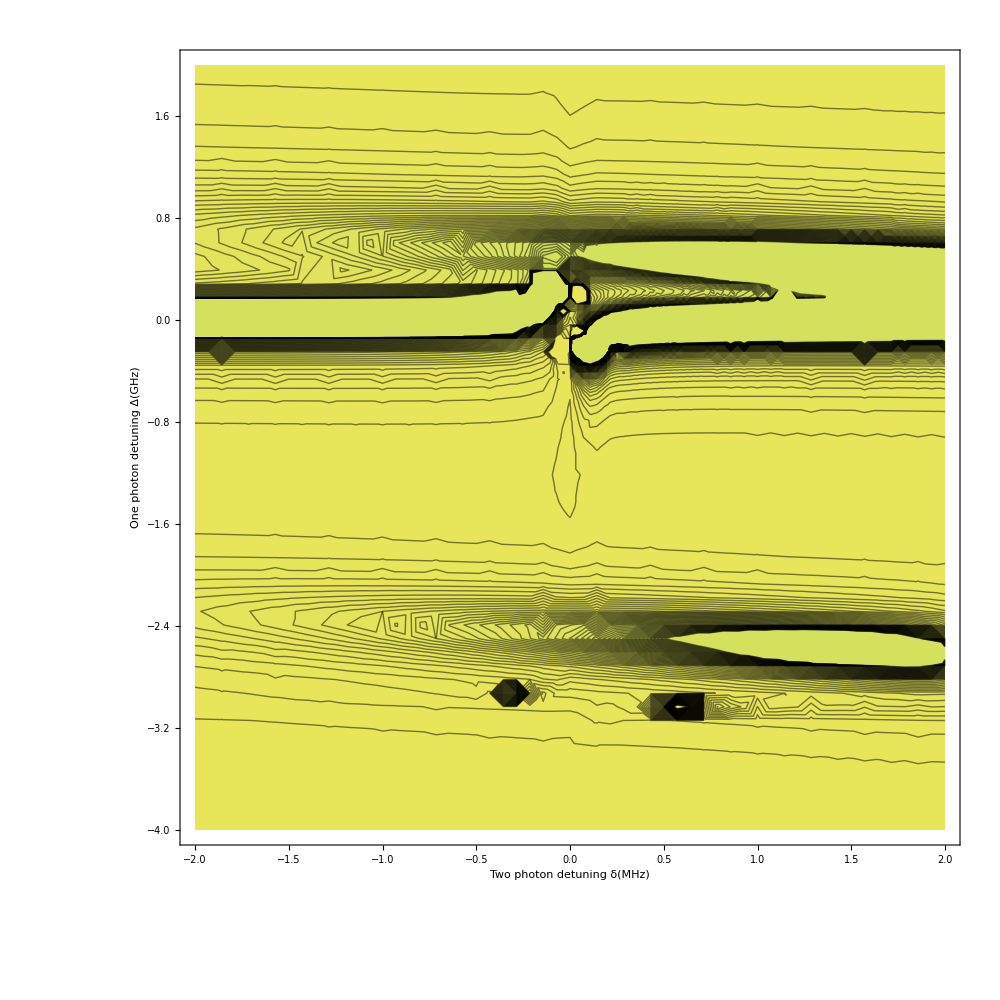

```mathematica
hhi1i=Interpolation[Flatten[Table[
Transpose[Flatten[{{Table[δ,{i,1,6001}]},Transpose[Eitw02[60,0.1/1000,100/1000,1/1000,0*10^6,δ*10^9]]},1]],{δ,-2,2,0.1}],1]]
datra88=ContourPlot[hhi1i[x,y],{x,-2,2},{y,-4,2},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,Contours->50,ImageSize->1000,FrameLabel->{Style["Two photon detuning δ(MHz)",13,Black],Style["One photon detuning Δ(GHz)",13,Black]},ClippingStyle->Automatic]
```

```mathematica
Manipulate[
ListPlot[Eitw02[60,pp/1000,pr/1000,1/1000,10*10^6,δ*10^9],PlotRange->{0,1},Joined->True]
,{δ,-2,2},{pr,0,1000},{pp,0,1000}]
```